# WHAM dispersion analysis (radial or axial - choose at the bottom)

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

{0.56,74.839}

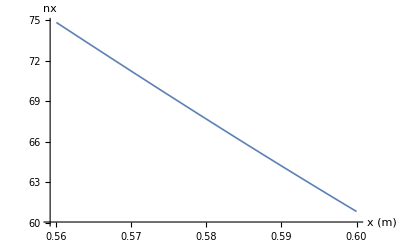

dataSet=wham

xProfileMin=0.56

xProfileMax=0.6

nXmin=30000000000000000000

nXmax=30000000000000000000

BXmin=0.845488

BXmax=15.7677

freq=25

nz=4

etaList={0.,1.,0.,0.,0.}

xmin=0.56

xmax=0.6

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
N[nt[[1]]]
PPComplexListPlot[nt,"x (m)","nx"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

## Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (i.e. fast and slow)

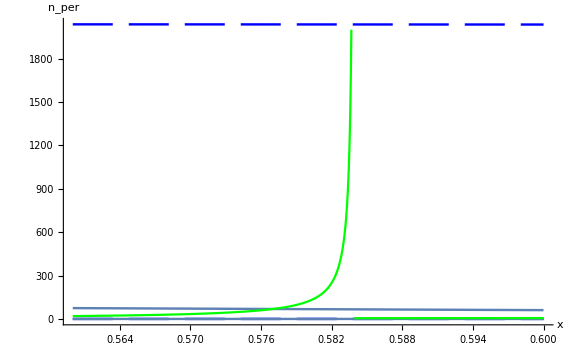

-Graphics-

dataSet=wham

xProfileMin=0.56

xProfileMax=0.6

nXmin=30000000000000000000

nXmax=30000000000000000000

BXmin=0.845488

BXmax=15.7677

freq=25

nz=4

etaList={0.,1.,0.,0.,0.}

xmin=0.56

xmin=0.56

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		ColdDis2FS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"x (m)","nx"];
g2=PPComplexListPlot[nS,"x (m)","nx"];

xx= Transpose[nS][[1]];
reF=( Re[Transpose[nF][[2]]]);
imF=( Im[Transpose[nF][[2]]]);
reS=( Re[Transpose[nS][[2]]]);
imS=( Im[Transpose[nS][[2]]]);
reSqF=(reF^2 - imF^2);
imSqF = 2*reF*imF;
reSqS=(reS^2 - imS^2);
imSqS = 2*reS*imS;

thickness=0.01;
(*d1=ListLinePlot[{Transpose[{xx,reSqF}],Transpose[{xx,imSqF}],Transpose[{xx,reSqS}],Transpose[{xx,imSqS}]},PlotStyle->{{Black,Thickness[thickness],Opacity[0.5]},{Black,Dashed,Thickness[thickness],Opacity[0.5],CapForm["Butt"]},{Red,Thickness[thickness],Opacity[0.5]},{Red,Dashed,Thickness[thickness],Opacity[0.5],CapForm["Butt"]}},(*ScalingFunctions->"Log",*)PlotLegends->{"re(fast)[cold]","im(fast)[cold]","re(slow)[cold]","im(slow)[cold]"},AxesLabel->{"axial pos [m]","k_per [1/m]"},LabelStyle->"Subtitle" ];
Show[{d1,dh},ImageSize->Large, PlotRange->{0,3000}]*)

Show[{g1,g2,dh}, PlotRange->All,AxesOrigin->{0.5,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]
Show[{g1,g2,dh}, PlotRange->All,AxesOrigin->{0.5,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

dataSet=wham

xProfileMin=0.56

xProfileMax=0.6

nXmin=30000000000000000000

nXmax=30000000000000000000

BXmin=0.845488

BXmax=15.7677

freq=25

nz=4

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=0.56

xmax=0.6

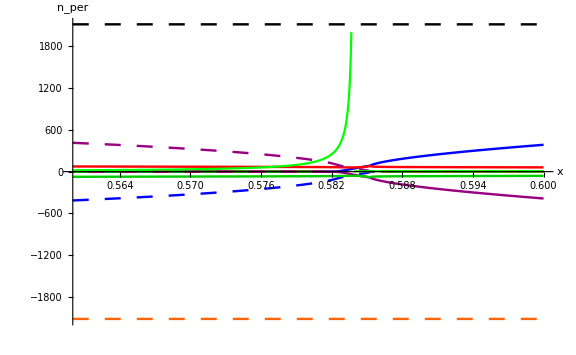

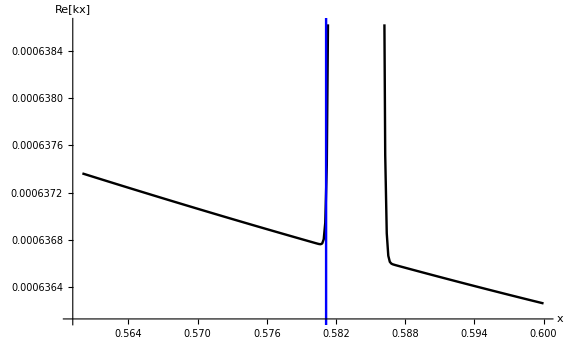

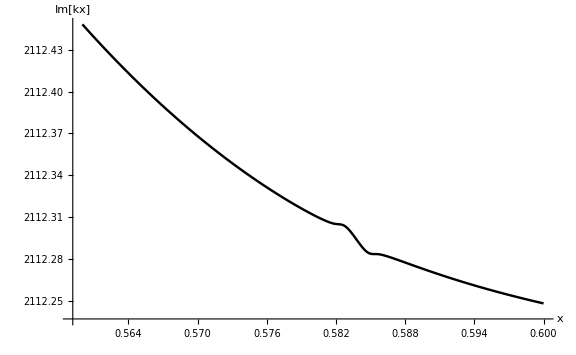

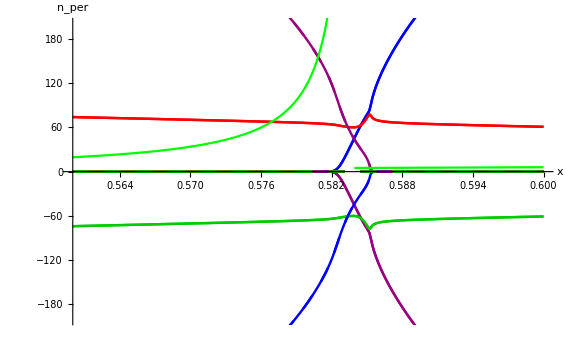

^3

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},x0=x;ne=nprof[x0];b=bprof[x0];TL=tprof[x0] *TList; WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];
rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

(*MatrixForm[rootsRe];
xx=rootsRe[[All,1]];
reR1=(rootsRe[[All,2]]);
reR2=( rootsRe[[All,3]]);
reR3=( rootsRe[[All,4]]);
reR4=( rootsRe[[All,5]]);
reR5=( rootsRe[[All,6]]);
reR6=( rootsRe[[All,7]]);
imR1=( rootsIm[[All,2]]);
imR2=( rootsIm[[All,3]]);
imR3=( rootsIm[[All,4]]);
imR4=( rootsIm[[All,5]]);
imR5=( rootsIm[[All,6]]);
imR6=( rootsIm[[All,7]]);

reSqR1 = reR1^2 - imR1^2;
reSqR2 = reR2^2 - imR2^2;
reSqR3 = reR3^2 - imR3^2;
reSqR4 = reR4^2 - imR4^2;
reSqR5 = reR5^2 - imR5^2;
reSqR6 = reR6^2 - imR6^2;

imSqR1 = 2*reR1*imR1;
imSqR2 = 2*reR2*imR2;
imSqR3 = 2*reR3*imR3;
imSqR4 = 2*reR4*imR4;
imSqR5 = 2*reR5*imR5;
imSqR6 = 2*reR6*imR6;


d2=ListLinePlot[{Transpose[{xx,reSqR1}],Transpose[{xx,reSqR2}],Transpose[{xx,reSqR3}],Transpose[{xx,reSqR4}],Transpose[{xx,reSqR5}],Transpose[{xx,reSqR6}],
Transpose[{xx,imSqR1}],Transpose[{xx,imSqR2}],Transpose[{xx,imSqR3}],Transpose[{xx,imSqR4}],Transpose[{xx,imSqR5}],Transpose[{xx,imSqR6}]},
PlotStyle->{{Purple},{Purple},{Purple},{Purple},{Purple},{Purple},{Dashed,Purple},{Dashed,Purple},{Dashed,Purple},{Dashed,Purple},{Dashed,Purple},{Dashed,Purple}},
(*ScalingFunctions->"Log",*)PlotRange->All, PlotLegends->{"re(warm)","re(warm)","re(warm)","re(warm)","re(warm)","re(warm)","im(warm)",
"im(warm)","im(warm)","im(warm)","im(warm)","im(warm)"}];
Show[{d2,dh},ImageSize->Large, PlotRange->{-2000,2000}]*)

g6=ComplexVectorListPlot[roots,"x (m)","nx"];

paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[{g6,dh},AxesOrigin->{0.56,0.},PlotRange->All, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]
g7=ComplexVectorListPlot[rootsRe, "x", "Re[kx]"]
g8 =ComplexVectorListPlot[rootsIm, "x", "Im[kx]"]
Show[{g6,g7,g8,dh}, PlotRange->{-200,200},AxesOrigin->{0.56,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]
```

## Now Try with Hot Plasma Dispersion using root finder

```mathematica
nPerpHot[x_,nxGuess_]:=Module[{ne,b,x0,TL,nx0},
		x0=x;
nx0=nxGuess;
     ne=nprof[x0];
b=bprof[x0];
     TL=tprof[x0]*TList;
rootRule=FindRoot[DisFuncGeneral[freq,ne,b,nz,nx,etaList,TL,nminList,nmaxList,modelList],{nx,nx0}, MaxIterations->50];
nx/.rootRule]
```

### First try root finding on warm plasma dispersion rel (model = 1)

```mathematica
modelList =Table[1,{i,1,6}];
```

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

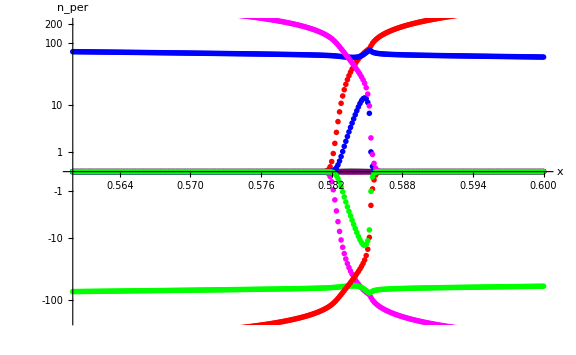

dataSet=wham

ne0=ne0

nsep=nsep

B=B

freq=25

nz=4

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={1,1,1,1,1,1}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

```mathematica
nxhot[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,nPerpHot[x0,nxGuess]};),{i,1,nPoints}];
nxH];

(*MatrixForm[nxhot[1]];
xx=nxhot[1][[All,1]];
reR1=Re[nxhot[1][[All,2]]];
imR1=Im[nxhot[1][[All,2]]];
reR2=Re[nxhot[2][[All,2]]];
imR2=Im[nxhot[2][[All,2]]];
reR3= Re[nxhot[3][[All,2]]];
imR3=Im[nxhot[3][[All,2]]];
reR4=Re[nxhot[4][[All,2]]];
imR4=Im[nxhot[4][[All,2]]];
reR5=Re[nxhot[5][[All,2]]];
imR5= Im[nxhot[5][[All,2]]];
reR6= Re[nxhot[6][[All,2]]];
imR6= Im[nxhot[6][[All,2]]];

reSqR1 = reR1^2 - imR1^2;
reSqR2 = reR2^2 - imR2^2;
reSqR3 = reR3^2 - imR3^2;
reSqR4 = reR4^2 - imR4^2;
reSqR5 = reR5^2 - imR5^2;
reSqR6 = reR6^2 - imR6^2;

imSqR1 = 2*reR1*imR1;
imSqR2 = 2*reR2*imR2;
imSqR3 = 2*reR3*imR3;
imSqR4 = 2*reR4*imR4;
imSqR5 = 2*reR5*imR5;
imSqR6 = 2*reR6*imR6;
symsize=8;
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};
d3=ListPlot[{Transpose[{xx,reSqR1}],Transpose[{xx,reSqR2}],Transpose[{xx,reSqR3}],Transpose[{xx,reSqR4}],Transpose[{xx,reSqR5}],Transpose[{xx,reSqR6}],Transpose[{xx,imSqR1}],Transpose[{xx,imSqR2}],Transpose[{xx,imSqR3}],Transpose[{xx,imSqR4}],Transpose[{xx,imSqR5}],Transpose[{xx,imSqR6}]},PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},PlotMarkers->{{"R",symsize},{"R",symsize},{"R",symsize},{"R",symsize},{"R",symsize},{"R",symsize},{"O",symsize},{"O",symsize},{"O",symsize},{"O",symsize},{"O",symsize},{"O",symsize}},PlotRange->{{0.,1.0},{-120,120}},AxesOrigin->{0.,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]},ScalingFunctions->symlog];
Show[{d3}] 
Show[{d3,dh}]*)
MatrixForm[nxhot[1]];
xx=nxhot[1][[All,1]];
reR1=Re[nxhot[1][[All,2]]];
imR1=Im[nxhot[1][[All,2]]];
reR2=Re[nxhot[2][[All,2]]];
imR2=Im[nxhot[2][[All,2]]];
reR3=Re[nxhot[3][[All,2]]];
imR3=Im[nxhot[3][[All,2]]];
reR4=Re[nxhot[4][[All,2]]];
imR4=Im[nxhot[4][[All,2]]];
reR5=Re[nxhot[5][[All,2]]];
imR5=Im[nxhot[5][[All,2]]];
reR6=Re[nxhot[6][[All,2]]];
imR6=Im[nxhot[6][[All,2]]];
symsize1=10;
symsize2=6;
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};

d3=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->{{0.56,0.6},{-200,200}},AxesOrigin->{0.56,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]},ScalingFunctions->symlog,
Epilog->{(*add vertical lines*)InfiniteLine[{2.0,0},{0,1}](*,InfiniteLine[{2.0,0},{0,1}],InfiniteLine[{0.5789109117254181,0},{0,1}]*)}];
Show[{d3}] 
(*g7=ComplexVectorListPlot[nxhot[1]^2,"x (m)","nx"];
g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];
g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];
g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12,dh},PlotRange->{-200,200},AxesOrigin->{1.9.,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]*)
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

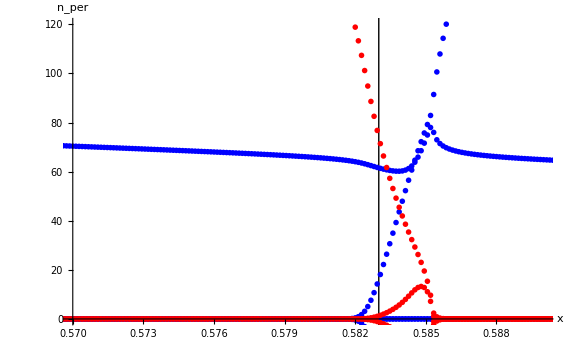

```mathematica
d3=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Blue},{Blue},{Blue},{Blue},{Blue},{Blue},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed,Red},{Dashed, Red}},
PlotMarkers->{{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize1},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2},{"o",symsize2}},
PlotRange->{{0.57,0.59},{0,120}},AxesOrigin->{0.57,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]},(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{0.583,0},{0,1}](*,InfiniteLine[{2.0,0},{0,1}],InfiniteLine[{0.5789109117254181,0},{0,1}]*)}];
Show[{d3}]
```

#### Now try with hot plasma (model = 2) for all species. Can I find the warm plasma roots with the full dispersion relation?

```mathematica
xPoint=0.;
guesses=nPerpWarm6[xPoint]  (* Warm plasma roots at x=0  *)
```

General::munfl: Exp[-7.15781×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.78756×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.79513×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00064288+2116.28 ⅈ,5.10505×10^-7-770.416 ⅈ,126.659+8.95751×10^-9 ⅈ,-0.00064288-2116.28 ⅈ,-5.10505×10^-7+770.416 ⅈ,-126.659-8.95751×10^-9 ⅈ}

Change model to 2

```mathematica
modelList =Table[2,{i,1,6}];
```

```mathematica
{nPerpHot[xPoint,guesses[[1]]],
nPerpHot[xPoint,guesses[[2]]],
nPerpHot[xPoint,guesses[[3]]],
nPerpHot[xPoint,guesses[[4]]],
nPerpHot[xPoint,guesses[[5]]],
nPerpHot[xPoint,guesses[[6]]]}
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}];
```

General::munfl: Exp[-1.78756×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.79513×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-384706.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

{0.00076299+1781.37 ⅈ,-1.26223×10^-8-731.723 ⅈ,126.617+8.94748×10^-9 ⅈ,-0.00076299-1781.37 ⅈ,1.26223×10^-8+731.723 ⅈ,-126.617-8.94748×10^-9 ⅈ}

dataSet=wham

ne0=ne0

nsep=nsep

B=B

freq=25

nz=4

etaList={0.,1.,0.,0.,0.}

TList={1.,0.,1.,0.,0.,0.}

modelList={2,2,2,2,2,2}

rmaj=rmaj

rmin=rmin

rsep=rsep

sol=sol

alphan=alphan

alphaT=alphaT

Hot plasma root finder gets all roots.  What about at xmin?

Hot plasma root finder gets 2 of the roots

### Plot hot plasma vs x

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

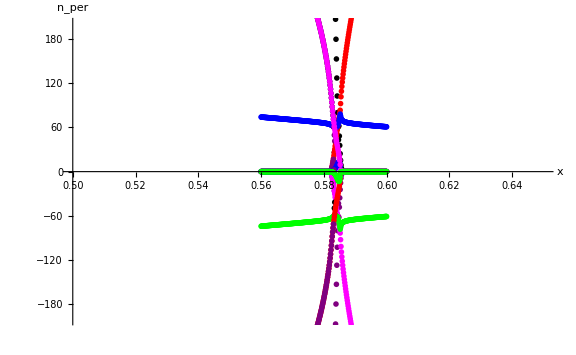

```mathematica
MatrixForm[nxhot[1]];
xx=nxhot[1][[All,1]];
reR1=( Re[nxhot[1][[All,2]]]);
imR1=( Im[nxhot[1][[All,2]]]);
reR2=( Re[nxhot[2][[All,2]]]);
imR2=( Im[nxhot[2][[All,2]]]);
reR3=( Re[nxhot[3][[All,2]]]);
imR3=( Im[nxhot[3][[All,2]]]);
reR4=( Re[nxhot[4][[All,2]]]);
imR4=( Im[nxhot[4][[All,2]]]);
reR5=( Re[nxhot[5][[All,2]]]);
imR5=( Im[nxhot[5][[All,2]]]);
reR6=( Re[nxhot[6][[All,2]]]);
imR6=( Im[nxhot[6][[All,2]]]);

reSqR1 = reR1^2 - imR1^2;
reSqR2 = reR2^2 - imR2^2;
reSqR3 = reR3^2 - imR3^2;
reSqR4 = reR4^2 - imR4^2;
reSqR5 = reR5^2 - imR5^2;
reSqR6 = reR6^2 - imR6^2;

imSqR1 = 2*reR1*imR1;
imSqR2 = 2*reR2*imR2;
imSqR3 = 2*reR3*imR3;
imSqR4 = 2*reR4*imR4;
imSqR5 = 2*reR5*imR5;
imSqR6 = 2*reR6*imR6;


symsize1=10;
symsize2=8;
symlog={Function[x,Sign[x] (Log[Abs[x]+1])],Function[y,Sign[y] (Exp[Abs[y]]-1)]};

d4=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->{{0.5,0.65},{-200,200}},AxesOrigin->{0.5,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]},(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{2.0,0},{0,1}](*,InfiniteLine[{2.0,0},{0,1}],InfiniteLine[{0.5789109117254181,0},{0,1}]*)}];
Show[{d4}] 
(*g7=ComplexVectorListPlot[nxhot[1]^2,"x (m)","nx"];
g8=ComplexVectorListPlot[nxhot[2],"x (m)","nx"];
g9=ComplexVectorListPlot[nxhot[3],"x (m)","nx"];
g10=ComplexVectorListPlot[nxhot[4],"x (m)","nx"];
g11=ComplexVectorListPlot[nxhot[5],"x (m)","nx"];
g12=ComplexVectorListPlot[nxhot[6],"x (m)","nx"];
Show[{g7,g8,g9,g10,g11,g12,dh},PlotRange->{-200,200},AxesOrigin->{0.,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]}]
paramPrint[{dataSet,ne0,nsep,B,freq,nz,etaList,TList,modelList,rmaj,rmin,rsep,sol,alphan,alphaT}]; *)
```

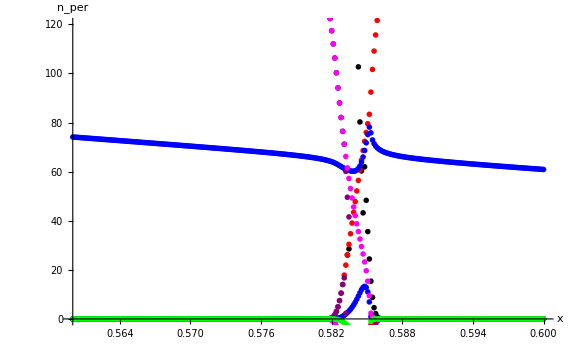

```mathematica
d4=ListPlot[{Transpose[{xx,reR1}],Transpose[{xx,reR2}],Transpose[{xx,reR3}],Transpose[{xx,reR4}],Transpose[{xx,reR5}],Transpose[{xx,reR6}],
Transpose[{xx,imR1}],Transpose[{xx,imR2}],Transpose[{xx,imR3}],Transpose[{xx,imR4}],Transpose[{xx,imR5}],Transpose[{xx,imR6}]},
PlotStyle->{{Black},{Red},{Blue},{Purple},{Magenta},{Green},{Dashed,Black},{Dashed,Red},{Dashed,Blue},{Dashed,Purple},{Dashed,Magenta},{Dashed, Green}},
PlotMarkers->{{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"R",symsize1},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2},{"O",symsize2}},
PlotRange->{{0.56,0.6},{0,120}},AxesOrigin->{0.56,0.}, ImageSize->Large,TicksStyle->Large,AxesLabel->{Style["x",FontSize->24],Style["n_per",FontSize->24]},(*ScalingFunctions->symlog,*)
Epilog->{(*add vertical lines*)InfiniteLine[{2.0,0},{0,1}](*,InfiniteLine[{2.0,0},{0,1}],InfiniteLine[{0.5789109117254181,0},{0,1}]*)}];
Show[{d4}]
```

## Focus on the damping

```mathematica
nxhotIm[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,Im[nPerpHot[x0,nxGuess]]};),{i,1,nPoints}];
nxH];
```

#### X - mode

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

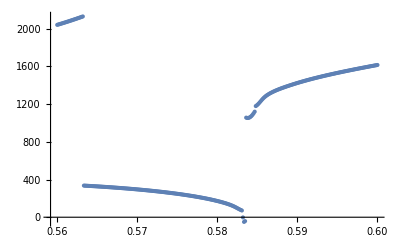

```mathematica
ListPlot[nxhotIm[1]]
```

### O - mode

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

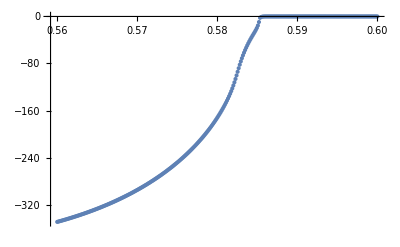

General::munfl: Exp[-2.11817×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.29217×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.30519×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

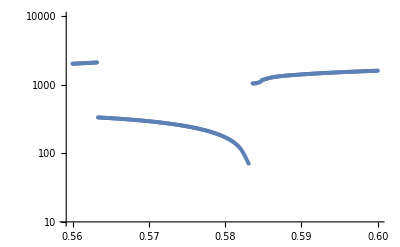

```mathematica
ListPlot[nxhotIm[2]]
ListPlot[{nxhotIm[1],nxhotIm[2]},ScalingFunctions->"Log",PlotRange->{10,10000}]
```

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

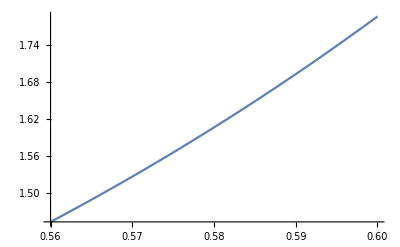

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

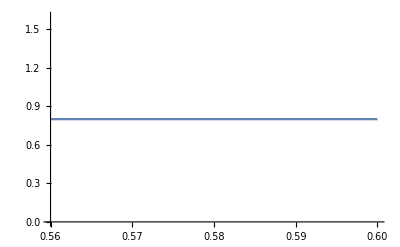

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

## Initialization

#### Magnetic field,Density and Temperature Profiles

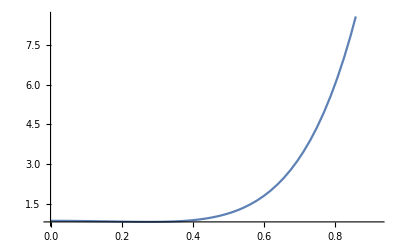

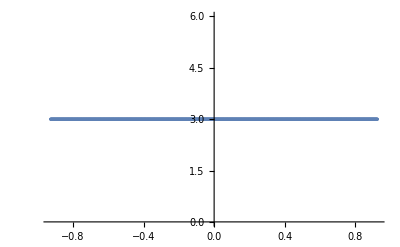

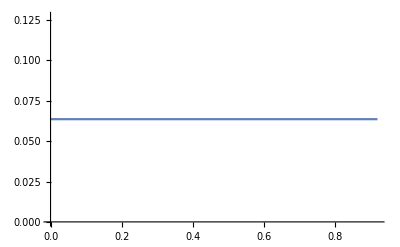

-Graphics-

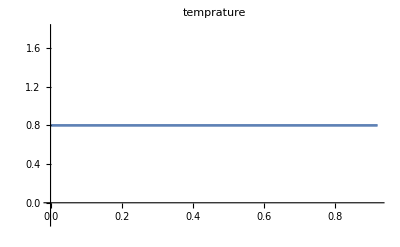

1.45328

1.78654

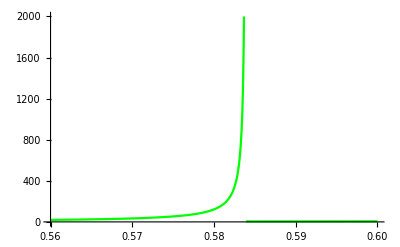

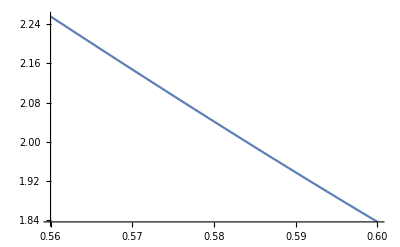

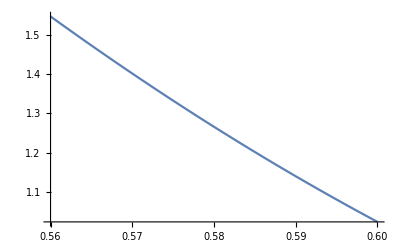

```mathematica
bprof2[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
nprof2[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
tprof2[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];

(* Radial profiles *)

(*dat=Import["/Users/dg6/code/dispersioneering-Mathematica/WHAM/WHAM_profiles_1Dradial.csv"];
datNoHeader=dat[[2;;,All]];
r=datNoHeader[[All,1]];
z=datNoHeader[[All,2]];
psi=datNoHeader[[All,3]];
nm3=datNoHeader[[All,4]];
TkeV=datNoHeader[[All,5]]*0.001;
BT=datNoHeader[[All,6]];
bprof:=ListInterpolation[BT,r];
nprof:=ListInterpolation[nm3,r];
tprof:=ListInterpolation[TkeV,r];

pb1=ListPlot[{Transpose[{r,BT}]}];
pb2=Plot[bprof[x],{x,0,0.2}];
pb3=Plot[bprof2[x],{x,0,0.2}];
Show[pb1,pb2,pb3]

pn1=ListPlot[{Transpose[{r,nm3}]},ScalingFunctions->"Log"];
pn2=Plot[nprof[x],{x,0,0.2},ScalingFunctions->"Log"];
pn3=Plot[nprof2[x],{x,0,0.2},ScalingFunctions->"Log"];
Show[pn1,pn2,pn3]

pt1=ListPlot[{Transpose[{r,TkeV}]}];
pt2=Plot[tprof[x],{x,0,0.2}];
pt3=Plot[tprof2[x],{x,0,0.2}];
Show[pt1,pt2,pt3]*)

(* profiles to match Cornwall's slide 4 of 
https://docs.google.com/presentation/d/1_X2sE95ZC_BSNV8qgfcvUNYZN-vLOnAmOo9IZzacEc0/edit#slide=id.gb9a7481f86_1_6
*)
(*Clear[nprof,bprof,tprof]
bprof[x_]:=0.8;
tprof[x_]:=0.6;
nprof[x_]:=10^((x-xProfileMin)/(xProfileMax-xProfileMin)*2+18 );
xProfileMin
xProfileMax
nprof[{xProfileMin,xProfileMax}]
LogPlot[nprof[x],{x,xProfileMin,xProfileMax}]*)

(* Axial profiles *)
clear[nprof,bprof,tprof];

dat=Import["/Users/78k/Desktop/myRepos/dispersioneering-Mathematica/WHAM/WHAM_profiles_1Daxial.csv"];
datNoHeader=dat[[2;;,All]];
r=datNoHeader[[All,1]];
z=datNoHeader[[All,2]];
psi=datNoHeader[[All,3]];
nm3=datNoHeader[[All,4]];
TkeV=datNoHeader[[All,5]]*0.001;
BT=datNoHeader[[All,6]];
bprof:=ListInterpolation[BT,z];
(*bprof2[x_]:= 2.0/(x+1.5); (*Hot plasma case*) *)
(*bprof2[x_]:= 2.0/(x+0.1);(*Cold plasma case*) *)
bprof2[x_]:=(14.71 * x^6+0.0003099*x^5+4.654*x^4-0.000302*x^3-0.9664*x^2+2.809*10^-5*x+0.845); (*WHAM*)
nprof[x_]:= x*0+3.1791 10^19;  (*ListInterpolation[nm3,z];*)(* ListInterplation seems to have trouble for flat data *)
tprof[x_]:= x*0+0.8; (* ListInterpolation[TkeV,z];*)
(*density profile calculation *)
q    =1.6 10^-19;
mi  =2 1.67 10^-27;
me  = 9.1*10^-31;
ep0= 8.854*10^-12;
wci = q*bprof[x]/mi;
w = freq*2*Pi*10^6;
R    = 0.9 (*(wpe/wce)^2*);
(*nprof[x_]:= R*ep0*bprof2[x]^2/me; (* ListInterplation seems to have trouble for flat data *)
tprof[x_]:=x*0+5.1; (* ListInterpolation[TkeV,z]; *)*)
Dimensions[BT];
Dimensions[z];
MatrixForm[Transpose[{z,BT}]];

pb1=ListPlot[{Transpose[{z,BT}]}];
pb2=Plot[bprof[x],{x,0,0.92}];
pb3=Plot[bprof2[x],{x,0,0.92}];
Show[pb3]

pn1=ListPlot[{Transpose[{z,nm3/(1 10^19) }]}] (* the ListPlot fails on such large numbers for flat plots for some reason *)
pn2=Plot[nprof[x]/(5 10^20),{x,0,0.92}];
(*pn3=Plot[nprof2[x]/(3.181 10^15),{x,-0.92,0.92}];*)
Show[pn2]

(*pn1=ListPlot[{Transpose[{z,nm3/(1 10^19) }]}]; *)(* the ListPlot fails on such large numbers for flat plots for some reason *)
pn2=Plot[nprof[x]/(1 10^19),{x,-0.92,0.92}];
pn3=Plot[nprof2[x]/(1 10^19),{x,-0.92,0.92}];
Show[pn1]


pt1=ListPlot[{Transpose[{z,TkeV}]}];
pt2=Plot[tprof[x],{x,0,0.92}];
pt3=Plot[tprof2[x],{x,0,0.92}];
Show[pt2,pt3,PlotRange->All,PlotLabel->"temprature"]

(* uncomment below to used linear profiles *)

bprof:=bprof2;
bprof[xProfileMin]
bprof[xProfileMax]

nprof:=nprof2;
tprof:=tprof2;

wci = q*bprof[x]/mi;
wce = q*bprof[x]/me;
wpe=Sqrt[(nprof[x]*q^2)/(ep0*me)];
dh=Plot[(5)/Mod[Abs[(1-w/wci)],1],{x,xProfileMin,xProfileMax},PlotRange->{0.01,2*10^3},(*ScalingFunctions->"Log",*)PlotStyle->Green];
Show[dh] 
Plot[w/wci,{x,xProfileMin,xProfileMax}]
Plot[(wpe/wce)^2,{x,xProfileMin,xProfileMax}]
```